## Mittelwert-Interpolation

### Worst Cases

Die blauen Punkte stellen die gesampleten Werte dar, die violetten die interpolierten. Anstatt eine Zick-Zack-Linie wird eine gerade erkannt. Es ist zu erwähnen, dass dieser Effekt als Glättung gewünscht sein könnte.

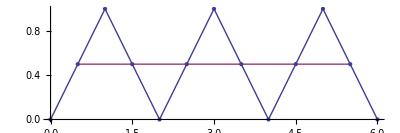

```mathematica
badSource={{0,0},{1,1},{2,0},{3,1},{4,0},{5,1},{6,0}};
badInterpolation = MovingAverage[N@badSource,2];
ListLinePlot[{badSource, badInterpolation}, Mesh->All, AspectRatio->1/3]
```

```mathematica
avgSource=Take[RandomInteger[50,{50,2}],10];
avgInterpolation = MovingAverage[N@avgSource,2];
ListLinePlot[{avgSource, avgInterpolation}, Mesh->All]
```

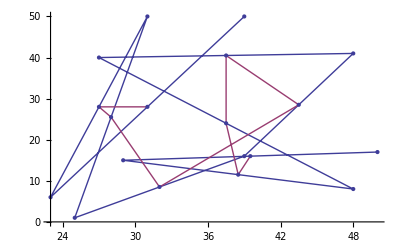

```mathematica
{{50,17},{29,15},{48,8},{27,40},{48,41},{39,16},{25,1},{31,50},{23,6},{39,50}}
```

### Normal Case

Im Normalfall ist es so, dass schlicht und einfach Ecken geglättet werden, da die Auflösung mit 40ms genug hoch ist.

{{0,0},{1,1/(√2)},{2,1},{3,1/(√2)},{4,0},{5,-1/(√2)},{6,-1},{7,-1/(√2)},{8,0}}

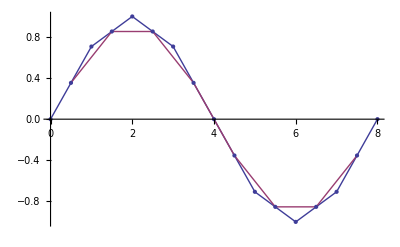

```mathematica
curveSource={{0,0},{1,1/(√2)},{2,1},{3,1/(√2)},{4,0},{5,-1/(√2)},{6,-1},{7,-1/(√2)},{8,0}}
curveInterpolation=MovingAverage[curveSource,2];
ListLinePlot[{curveSource, curveInterpolation}, Mesh->All]
```